# Pubmed baseline 2023 summary

## Definition

```mathematica
exportdocdir="/Users/kouamano/gitsrc/pubmed-analysis/202312/"
```

/Users/kouamano/gitsrc/pubmed-analysis/202312/

### terms

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/defs.wl"]//TableForm
```

高被引用論文 | 被引用数全体の1%を構成する被引用数上位論文。
高被引用論文掲載誌 | 高被引用論文を出版した雑誌。
高被引用テーマ | 高被引用論文に付与されるMeSHディスクリプター。
高被引用論文引用テーマ | 高被引用論文を引用する論文に付与されるMeSHディスクリプター。
研究テーマ | 論文に付与されるMeSHディスクリプター。
引用テーマ | 論文を引用する論文に付与されるMeSHディスクリプター。

### generation

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/generations.wl"]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
period
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
periodticks
```

{{1,1950},{2,1955},{3,1960},{4,1965},{5,1970},{6,1975},{7,1980},{8,1985},{9,1990},{10,1995},{11,2000},{12,2005},{13,2010},{14,2015},{15,2020}}

```mathematica
gen
```

{1946-1950,1946-1955,1946-1960,1946-1965,1946-1970,1946-1975,1946-1980,1946-1985,1946-1990,1946-1995,1946-2000,1946-2005,1946-2010,1946-2015,1946-2020}

```mathematica
genR
```

{1946-1950,1946-1955,1946-1960,1946-1965,1946-1970,1946-1975,1946-1980,1946-1985,1946-1990,1946-1995,1946-2000,1946-2005,1946-2010,1946-2015,1946-2020}

```mathematica
genticks
```

{{1,1946-1950},{2,1946-1955},{3,1946-1960},{4,1946-1965},{5,1946-1970},{6,1946-1975},{7,1946-1980},{8,1946-1985},{9,1946-1990},{10,1946-1995},{11,1946-2000},{12,1946-2005},{13,1946-2010},{14,1946-2015},{15,1946-2020}}

```mathematica
genEnd
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

## 全期間、年、累積でない

### count of published articles (1971 ~ 2023)

```mathematica
pubyearTlySort["whole"]=Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearCount.wl"];
```

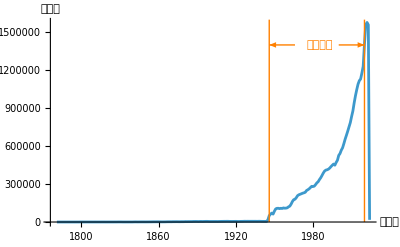

```mathematica
gr1=ListPlot[ToExpression[pubyearTlySort["whole"]],Joined->True,PlotRange->All,AxesLabel->{"出版年","収録数"},Epilog->{Orange,Line[{{1946,0},{1946,1.6 10^6}}],Line[{{2020,0},{2020,1.6 10^6}}],Arrow[{{1946+20,1.4 10^6},{1946,1.4 10^6}}],Arrow[{{2020-20,1.4 10^6},{2020,1.4 10^6}}],Text[Style["対象範囲"],{1985,1.4 10^6}]},ImageSize->400]
```

```mathematica
Export[exportdocdir<>"gr1.eps",gr1,"EPS"]
```

/Users/kouamano/gitsrc/pubmed-analysis/202312/gr1.eps

## 対象期間、世代、累積でない

### count of articles by gen (1950 ~ 2020)

```mathematica
artcountBygen=Map[Total,Partition[Map[#[[2]]&,pubyearTlySort["whole"][[163;;237]]],5]]
```

{331362,534892,549642,725868,1014763,1166703,1352292,1542151,1917765,2144518,2393705,2971542,3776593,4954484,6064352}

### count of references by gen (1950 ~ 2020)

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/refcountByGen.wl"]
```

{33832,148555,291655,445022,818629,1369688,1998678,2821649,4022714,5715689,6095491,9616790,27856034,63701319,98905026}

```mathematica
refcountBygen
```

{33832,148555,291655,445022,818629,1369688,1998678,2821649,4022714,5715689,6095491,9616790,27856034,63701319,98905026}

### count of articles that have reference by gen (1950 ~ 2020)

```mathematica
refArtcountBygen=Table[refArtcount[n],{n,1950,2020,5}]
```

{10389,24443,32643,44987,71330,101680,129636,159819,202028,246937,212576,315957,818095,1787173,2714514}

### count of cited articles by gen (from 1781 to 1950 ~ 2020)

```mathematica
citedArtcountBygen=Table[citedArtcount[n],{n,1950,2020,5}]
```

{18495,77552,146087,208781,338909,514990,726877,962280,1289322,1718646,1929649,2978737,5742485,9695229,13936302}

### count of ISSN by gen (1950 ~ 2020)

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/journal/ISSNvspubgenTly.save"];
```

```mathematica
(ISSNsBygen=Map[Flatten,Map[#[[1]]&,ISSNvspubgenTly["All"],{2}]])//Length
```

15

```mathematica
ISSNcountBygen=Map[Length,ISSNsBygen]
```

{1800,2179,2713,4039,5279,7421,9874,11783,13747,15589,18276,20441,25956,31209,35252}

### plot

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/generations.wl"]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
gr2=ListPlot[{ISSNcountBygen,artcountBygen,refcountBygen,refArtcountBygen,citedArtcountBygen},PlotLabels->{"雑誌数","登録論文数","引用数","参考文献を\n持つ論文数","引用された\n論文数"},Frame->True,FrameLabel->{"出版年","収録数"},FrameTicks->{Automatic,{periodticks,None}},PlotRange->Full,Joined->True,ImageSize->540]
```

-Graphics-

```mathematica
Export[exportdocdir<>"gr2.eps",gr2,"EPS"]
```

/Users/kouamano/gitsrc/pubmed-analysis/202312/gr2.eps

```mathematica
ListPlot[{ISSNcountBygen,artcountBygen,refcountBygen,refArtcountBygen,citedArtcountBygen},Axes->True,AxesLabel->{"出版年","収録数"},PlotLabels->{"雑誌数","登録論文数","引用数","参考文献を持つ論文数","引用された論文数"},Frame->True,FrameTicks->{Automatic,{periodticks,None}},PlotRange->Full,Joined->True]
```

-Graphics-

```mathematica
ISSNcountBygen
```

{1800,2179,2713,4039,5279,7421,9874,11783,13747,15589,18276,20441,25956,31209,35252}

```mathematica
artcountBygen
```

{331362,534892,549642,725868,1014763,1166703,1352292,1542151,1917765,2144518,2393705,2971542,3776593,4954484,6064352}

```mathematica
refcountBygen
```

{33832,148555,291655,445022,818629,1369688,1998678,2821649,4022714,5715689,6095491,9616790,27856034,63701319,98905026}

```mathematica
refArtcountBygen
```

{10389,24443,32643,44987,71330,101680,129636,159819,202028,246937,212576,315957,818095,1787173,2714514}

```mathematica
citedArtcountBygen
```

{18495,77552,146087,208781,338909,514990,726877,962280,1289322,1718646,1929649,2978737,5742485,9695229,13936302}